```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};

NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

hbar=197.327053;
Mm=938.92;
μ=3. Mm/4.;mh2=(2 μ)/(hbar)^2;
```

```mathematica
Integrate[Exp[-α x^2],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√π)/(√α),Re[α]>0]

```mathematica
legs=Simplify[Flatten[{TraditionalForm[SetPrecision[wfkt1,2]],TraditionalForm[SetPrecision[wfkt2,2]][[1]]}]]
```

{0.29 ⅇ^(-0.3 r^2),0.055 ⅇ^(-0.3 r^2)-0.055 ⅇ^(-0.03 r^2),-4.8 ⅇ^(-0.32 r^2)+4.8 ⅇ^(-0.3 r^2),-0.56 ⅇ^(-0.62 r^2)+0.56 ⅇ^(-0.3 r^2),-0.42 ⅇ^(-0.91 r^2)+0.42 ⅇ^(-0.3 r^2)}

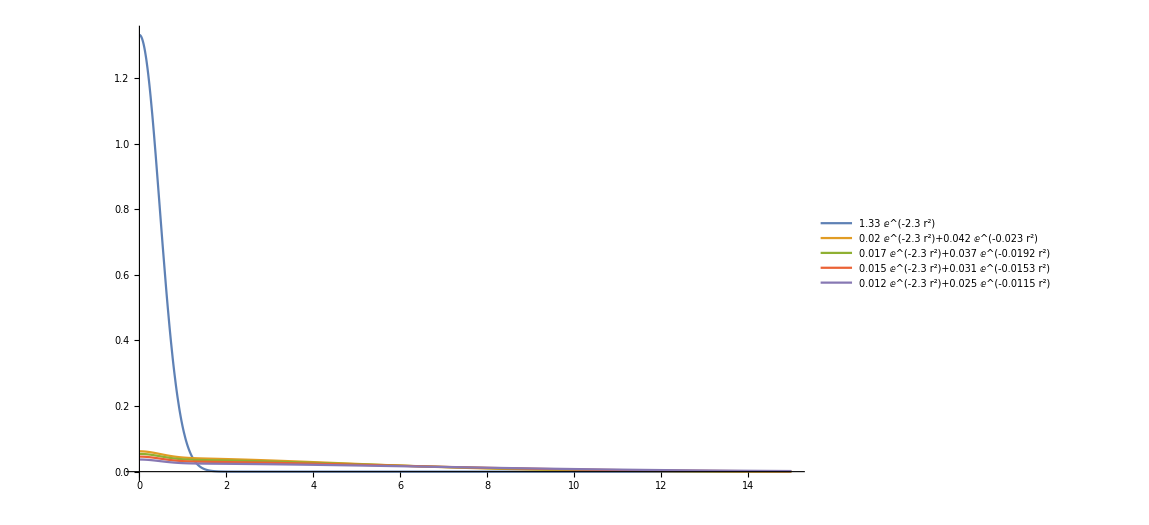

```mathematica
a1=2.3;
c2=2.1;
a2Range=Subdivide[0.01 a1,0.005 a1,3];
core1={{1.0,a1}};
core2={{1.0,a1},{c2,#}}&/@a2Range;
wfkt1=NormTF[core1] Total[#[[1]] Exp[-#[[2]] r^2]&/@core1];
wfkt2=Table[NormTF[core] Total[#[[1]] Exp[-#[[2]] r^2]&/@core],{core,core2}];
legs=Simplify[Flatten[{TraditionalForm[SetPrecision[wfkt1,3]],TraditionalForm[SetPrecision[wfkt2,3]][[1]]}]];
Plot[{wfkt1,wfkt2},{r,0,15},PlotRange->Full,ImageSize->850,PlotLegends->legs]
```

```mathematica
4 Pi Integrate[r^2 (NormTF[core1] Total[#[[1]] Exp[-#[[2]] r^2]&/@core1])^2,{r,0,20}]
4 Pi Integrate[r^2 (NormTF[core2] Total[#[[1]] Exp[-#[[2]] r^2]&/@core2])^2,{r,0,20}]
```

1.

1.

```mathematica
grid[x_,y0_,y1_,nn_,a_:1,b_:2]:=y1-(y0-y1)/((a/b)^nn-1)+(y0-y1)/(b^-nn-a^-nn) 1/x^nn;
```

```mathematica
Simplify[grid[x,y0,y1,nn,a,b]]/.{a->1,b->2}
```

(2^nn x^-nn (y0-y1))/(1-2^nn)+y1+(-y0+y1)/(-1+2^-nn)

{3,8,13}

{1.,1.09091,1.18182,1.27273,1.36364,1.45455,1.54545,1.63636,1.72727,1.81818,1.90909,2.}

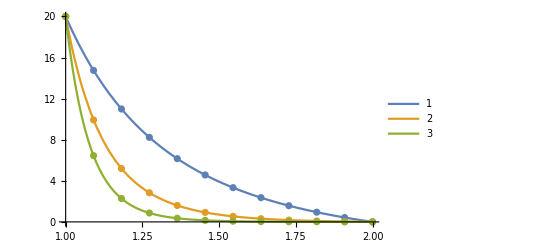

(0.001 | 0.428887 | 0.946667 | 1.57924 | 2.36028 | 3.33601 | 4.57108 | 6.15773 | 8.23049 | 10.9908 | 14.7489 | 20.
0.001 | 0.0363602 | 0.0906888 | 0.175981 | 0.313116 | 0.539534 | 0.924623 | 1.60184 | 2.83883 | 5.19855 | 9.93178 | 20.
0.001 | 0.0030285 | 0.00698742 | 0.0149783 | 0.0317191 | 0.0682741 | 0.151881 | 0.353355 | 0.868523 | 2.27839 | 6.45228 | 20.)

```mathematica
aa=1;bb=2;nbrW=12;
nmin=3;nmax=13;nbrSets=2;

rang=Subdivide[nmin,nmax,nbrSets]
grdX=N[Subdivide[aa,bb,nbrW-1]]
wMin=0.001;wMax=20;
grds=grid[x,wMin,wMax,#,aa,bb]&/@rang;
wds=grds/.x->grdX;
Show[Plot[grds,{x,aa,bb},PlotLegends->leg,PlotRange->Full],ListPlot[Transpose[{grdX,#}]&/@wds]]
Histogram[N[wds],400];
Reverse[#]&/@wds//MatrixForm
```

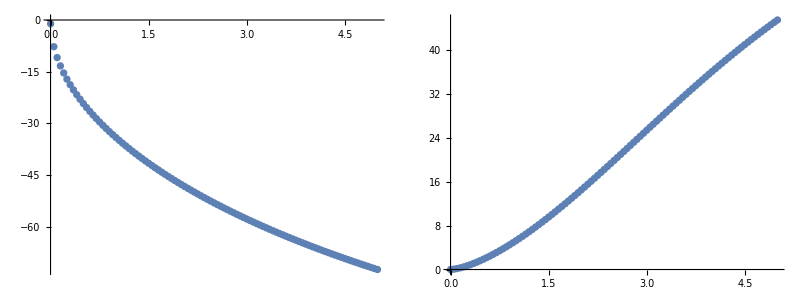

```mathematica
aSlimit=3.15;
rSlimit=2.02;
aPlimit=-13.44;
rPlimit=1.03;
eRange=Subdivide[0.001,5,100];

Sphase=(180./Pi) ArcCot[-1./(aSlimit Sqrt[2 μ #]/hbar)+0.5 rSlimit Sqrt[2 μ #]/hbar]&/@eRange;
Pphase=(180./Pi) ArcCot[-1./(aPlimit (Sqrt[2 μ #]/hbar)^3)+0.5 rPlimit/(Sqrt[2 μ #]/hbar)^2/hbar]&/@eRange;
Grid[{{
ListPlot[Transpose[{eRange,Sphase}],PlotRange->Full,AxesLabel->{MaTeX["E_{rel}",Magnification->2],MaTeX["\\delta_S(E)",Magnification->2]},ImageSize->Large],
ListPlot[Transpose[{eRange,Pphase}],PlotRange->Full,AxesLabel->{MaTeX["E_{rel}",Magnification->2],MaTeX["\\delta_P(E)",Magnification->2]},ImageSize->Large]
}}]
```